# Dinámica de la pureza de la matriz de Choi

Se estudia la dinámica de la pureza de la matriz de Choi para la cadena de espines de Wisniacki. 

Figs: fig:choi:purity:spin:chain:vs:goe, fig:choi:purity:dynamics

## Cargar paquetes y definiciones

```mathematica
(* Establecer que el directorio sea el mismo que el de este notebook *)
SetDirectory[NotebookDirectory[]]
```

/home/jadeleon/Documents/quantum_chaotic_channels/ja_files

```mathematica
(* Cargar paquetes QMB.wl y Chaometer.wl *)
Get["../Mathematica_packages/"<>#]&/@{"Chaometer.wl","QMB.wl"};
```

```mathematica
(* Ticks personalizados para las gráficas en escala log *)
labeledTicks=Table[{10^i,Superscript[10,i]},{i,-20,15}];
unlabeledTicks=Flatten[Table[{k*j,Null},{k,2,9},{j,labeledTicks[[All,1]]}],1];
myTicks=Join[labeledTicks,unlabeledTicks];
```

## 1. Cadena L=11 vs Hamiltoniano de GOE L=10

Se calcula la dinámica de la pureza de la matriz de Choi para la cadena de espines L=11 y para un Hamiltoniano de GOE de L=10.

v.1.0.	fig:choi:purity:spin:chain:vs:goe

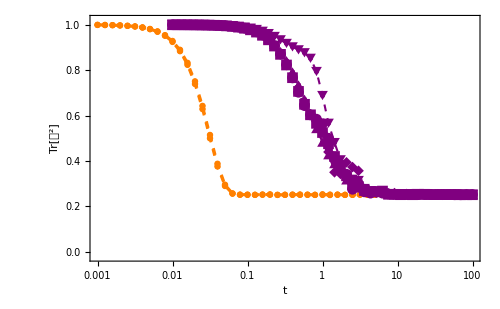

## 1.1. Cálculo de superoperadores del caómetro

Se calculan los superoperadores de los canales cuánticos a cada t entre 0.001 y 100 en escala log. Superoperadores exportados como “superoperators_#_t_log_scale.csv”.

### Parameters setup

```mathematica
L=11(*number of spins*);
{hx,hz,J}={1.,0.5,ConstantArray[1.,L-1]}(*hz=0.5 chaotic, hz=2.5 regular*)
```

{1.,0.5,{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvalsH,eigenvecsH}=N[Chop[Eigensystem[H]]];
]
```

```mathematica
(*Three initial random states of the environment Subscript[ψ, 0E]=Subscript[random, 1]⊗…⊗Subscript[random, L-1]*)
SeedRandom[32371];
ψ0E=Table[RandomChainProductState[L-1],5];
```

### Calculation of superoperators

```mathematica
superoperators={};
```

```mathematica
AbsoluteTiming[
Do[
AppendTo[superoperators,Superoperator[t,ψ0E[[5]],eigenvalsH,eigenvecsH,L]],
{t,10^Range[-2,2,0.08]}](* tiempos equiespaciados en escala log *)
]
```

{263.683,Null}

```mathematica
Export["/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/chaotic/superoperators_5_t_log_scale.csv",Prepend[superoperators,"L=11;{hx,hz,J}={1.,0.5,ConstantArray[1.,L-1]};SeedRandom[32371];ψ0E=Table[RandomChainProductState[L-1],3];Superoperator[t,ψ0E[[5]],eigenvalsH,eigenvecsH,L];"],"CSV"]
```

/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/chaotic/superoperators_5_t_log_scale.csv

## 1.2. Pureza de Choi del caómetro

```mathematica
(* Importar los datos de los superoperadores *)
superoperators=ToExpression[Import["chaotic/superoperators_"<>ToString[#]<>"_t_log_scale.csv"][[2;;]]]&/@Range[5];
```

```mathematica
(* Calcular las matrices de Choi *)
chois=1/2*Map[Reshuffle,superoperators,{2}];
```

```mathematica
(* Calcular la pureza de las matrices de Choi *)
choisPurity=Chop[Map[Purity,chois,{2}]];
```

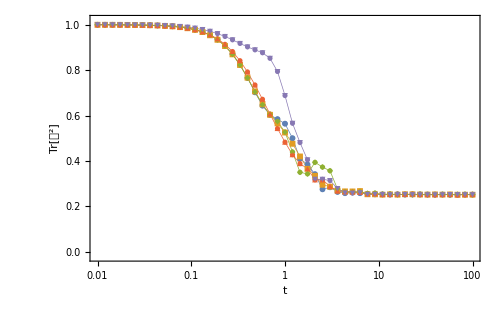

```mathematica
ListLogLinearPlot[
Transpose[{10^Range[-2,2,0.08],#}]&/@choisPurity,
PlotRange->{{10^(-2),100},{-0.02,1.02}},
Joined->True,
PlotMarkers->{Automatic,6},
PlotStyle->Directive[Thickness[0.001]],
Mesh->All,
GridLines->{Table[10^x,{x,-2,2}],Automatic},
GridLinesStyle->Directive[Gray,Dashed],
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t]],TraditionalForm[HoldForm[Tr[𝒟^2]]]},
FrameTicks->{{Automatic,None},{myTicks,None}},
LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->22],
ImageSize->500
]
```

## 1.3. Pureza de Choi de un Hamiltoniano de GOE L=10

```mathematica
L=10;
```

```mathematica
(* Calcular un Hamiltoniano de GOE y obtener sus eigenvalores y eigenvectores *)
Module[{H},
H=RandomVariate[GaussianOrthogonalMatrixDistribution[2^L]];
(*U=MatrixExp[-I H];*)
{eigenvalsH,eigenvecsH}=Chop[Eigensystem[H]];
]
```

```mathematica
(* Revisar que los eigenvectores esten normalizados *)
AllTrue[Norm/@eigenvecsH,#==1.&]
```

True

```mathematica
(* Definir un estado inicial para el entorno de L-1 espines *)
ψ0E=RandomChainProductState[L-1];
```

```mathematica
choiPurityGOE={};
```

```mathematica
(* Calcular la pureza de la matriz de Choi con eq:choi:chaometer:purity:1 *)
AbsoluteTiming[
AppendTo[choiPurityGOE,Table[
{t,
1/4*Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,q}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E],eigenvalsH,eigenvecsH]
]^2
,{i,2},{j,2},{p,2},{q,2}]}
,{t,10^Range[-3,2,0.1]}]];
]
```

{33.8267,Null}

## 1.4. Comparación en figuras

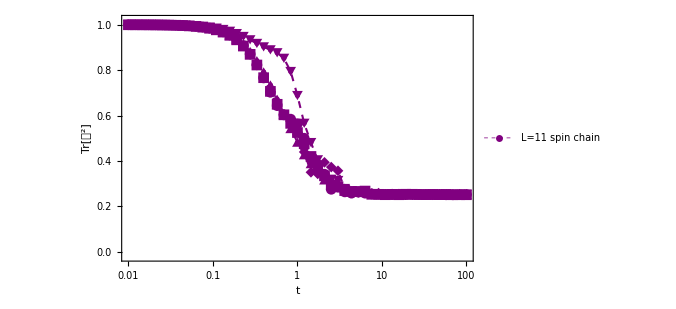

```mathematica
fig1=ListLogLinearPlot[
Transpose[{10^Range[-2,2,0.08],#}]&/@choisPurity,
PlotRange->{{10^(-2),100},{-0.02,1.02}},
Joined->True,
PlotMarkers->{Automatic,11},
PlotStyle->Directive[Purple,Thickness[0.003],Dashed],
Mesh->All,
GridLines->{Table[10^x,{x,-2,2}],Automatic},
GridLinesStyle->Directive[Gray,Dashed],
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t]],TraditionalForm[HoldForm[Tr[𝒟^2]]]},
FrameTicks->{{Automatic,None},{myTicks,None}},
LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->22],
ImageSize->500,
PlotLegends->Placed[LineLegend[{ToString[TraditionalForm[HoldForm[L=11]]]<>" spin chain"},LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->15]], {Right,Top}]
]
```

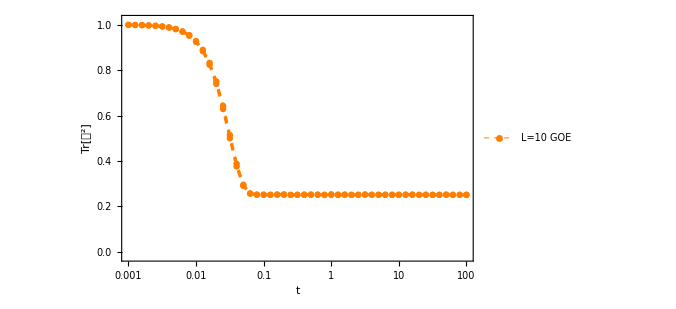

```mathematica
fig2=ListLogLinearPlot[
choiPurityGOE,
PlotRange->{{10^(-3),100},{-0.02,1.02}},
PlotMarkers->{"OpenMarkers",Medium},Joined->True,
PlotStyle->Directive[Orange,Dashed,Thickness[0.004]],
Mesh->All,
GridLines->{Table[10^x,{x,-2,2}],Automatic},
GridLinesStyle->Directive[Gray,Dashed],
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t]],TraditionalForm[HoldForm[Tr[𝒟^2]]]},
FrameTicks->{{Automatic,None},{myTicks,None}},
LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->22],
ImageSize->500,
PlotLegends->Placed[LineLegend[{ToString[TraditionalForm[HoldForm[L=10]]]<>" GOE"},LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->15]], {Right,Top}]
]
```

```mathematica
Show[fig2,fig1,PlotLegends->Automatic]
```

-Graphics-

## 2. Variando el tamaño de la cadena de espines

Se calcula la dinámica de la pureza de la matriz de Choi variando L de 3 a 10, para estados iniciales aleatorios del entorno.

v.1.0.	fig:choi:purity:dynamics

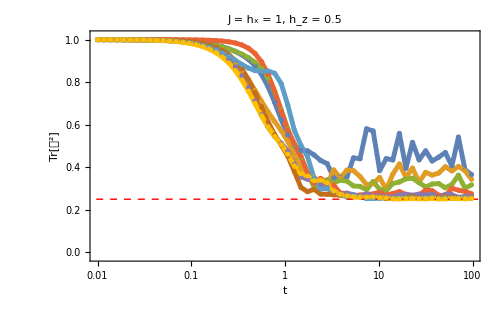
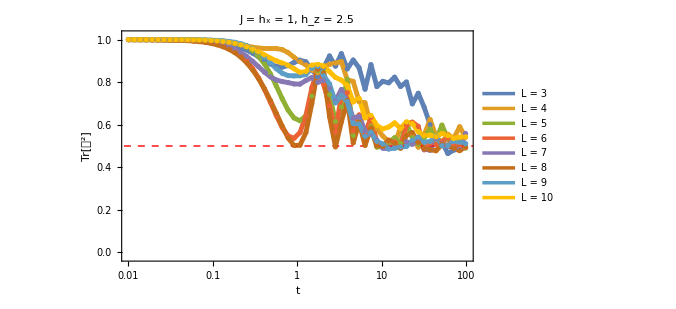

## 2.1. Cálculos

```mathematica
{Lmin,Lmax,tmin,tmax,step}={3,10,-2,2,0.07};(* tmin, tmax y step son los exponentes 10^t *)
choiPurity=Table[
(* Establecer valores de los parámetros del Hamiltoniano *)
{hx,hz,J}={1.,0.5,ConstantArray[1.,L-1]};(*hz=0.5 caótico, hz=2.5 regular*)

(* Obtener eigenvalores y eigenvectores del Hamiltoniano *)
Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvalsH,eigenvecsH}=N[Chop[Eigensystem[H]]];
]

(* Generar un estado aleatorio para el enotrno *)
ψ0E=RandomChainProductState[L-1];

(* Calcular el superoperador *)
superoperatorOfDynamicalMap=Table[Superoperator[t,ψ0E,eigenvalsH,eigenvecsH,L],{t,10^Range[tmin,tmax,step]}(* tiempos equiespaciados en escala log *)];

(* Calcular la matriz de Choi *)
choiOfDynamicalMap=1/2Reshuffle[#]&/@superoperatorOfDynamicalMap;

(* Calcular la pureza de la matriz de Choi *)
Purity/@choiOfDynamicalMap
,{L,Lmin,Lmax}];
```

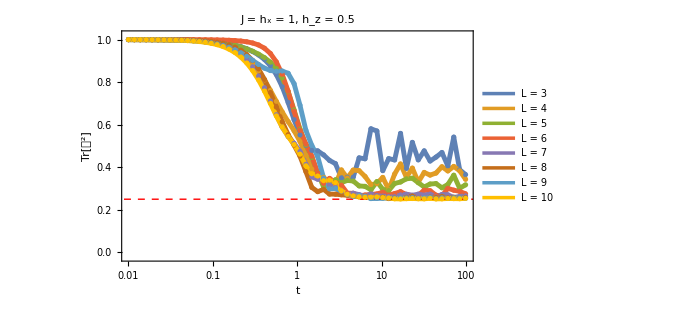

```mathematica
fig=ListLogLinearPlot[Transpose[{10^Range[tmin,tmax,step],#}]&/@choiPurity,
PlotRange->{{10^tmin,10^tmax},{-0.02,1.02}},
Joined->True,
(*PlotMarkers->{Automatic,11},*)
PlotStyle->Directive[Thickness[0.007]],
Mesh->All,
GridLines->{Table[10^x,{x,tmin,tmax}],Automatic},
GridLinesStyle->Directive[Gray,Dashed],
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t]],TraditionalForm[HoldForm[Tr[𝒟^2]]]},
FrameTicks->{{Automatic,None},{myTicks,None}},
LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->22],
ImageSize->500,
PlotLegends->Placed[LineLegend[Table["L = "<>ToString[L],{L,Lmin,Lmax}],LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->15]], Right],
Epilog->{Red,Thick,Dashed,InfiniteLine[{{10^tmin,0.25},{10^tmax,0.25}}]},
PlotLabel->Style["J = h_x = 1, h_z = "<>ToString[hz],Black,FontSize->22]
]
```